# Homework Problem 2

-Graphics-

## a) Analytically determine the non-negative steady states (fixed points) of the model (2).

As to find a fixed point in a discrete system  needs to be fulfilled. The trivial case  = 0 can be located as the first FP. When solving the equation for a  so that the condition  is fulfilled .

```mathematica
ClearAll["Global`*"];

eq = N == (r + 1)*N/(1 + (N/K)^b);
(* Find a numerical solution for N *)
sol = NSolve[eq, N]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{N→0.},{N→1. K r^(1/b)}}

## b) Perform linear stability analysis and discuss how the linear stability of the non-negative steady states depends on the parameters

Lets take the derivative of the model in regard of N and check the “slope” at the found fixed points

```mathematica
ClearAll["Global`*"];
f1[n_] := (r + 1) * n / (1 + (n/K)^b)
f2[n_] = D[f1[n],n] // Simplify
```

-((-1-(n/K)^b+b (n/K)^b) (1+r))/((1+(n/K)^b)^2)

First we evaluate the FP N1* = 0.

```mathematica
f2[0] // Simplify
```

-((-1-0^b+0^b b) (1+r))/((1+0^b)^2)

Further simplified one finds that the slope is .

Secondly  lets check the FP N2* =

```mathematica
f2[K*r^(1/b)] // Simplify
```

-((1+r) (-1-(r^(1/b))^b+b (r^(1/b))^b))/((1+(r^(1/b))^b)^2)

This  clears out to  , which describes the slope and therefore the stability.
Now to determine the stability we need to figure out it . In the first case the FP is unstable, in the second one stable.
For the FP1 N1* =  0, the slope of the linear approximation is , since  it follow that , we see that the system is unstable.
For the FP2 N2* = , the slope is takes the form  . We find a critical value for b, . In case of r = 0,  becomes 1. For values of the FP becomes stable, otherwise unstable.

## c) Analytically find all conditions on the parameters (within their ranges of validity) where a bifurcation from a stable steady state to an unstable steady state occurs.

As  described in subtask b), one finds a criticial depence of b in regard of r, . When b approaches  the stability of the FP changes.

## d) Investigate how the population size depends on time for the following val.02ues of the initial population size: N0 = 1, 2, 3 and 10. For each case, use the linear stability analysis performed in task b) to approximate the pop.02ulation dynamics in the vicinity of the unstable steady state. [Hint: treat the initial condition as a small perturbation around the unstable steady state, and plot how this perturbation, and consequently the population size, is expected to change over time according to the linear stability anal.02ysis.] Plot this approximation together with the corresponding (exact) population dynamics obtained by iterating Eq. (2). Use log-log scale for plotting to distinguish well between the different curves.

What  can  be  stated directly, as also already mentioned, in the case  the system is stable for all .

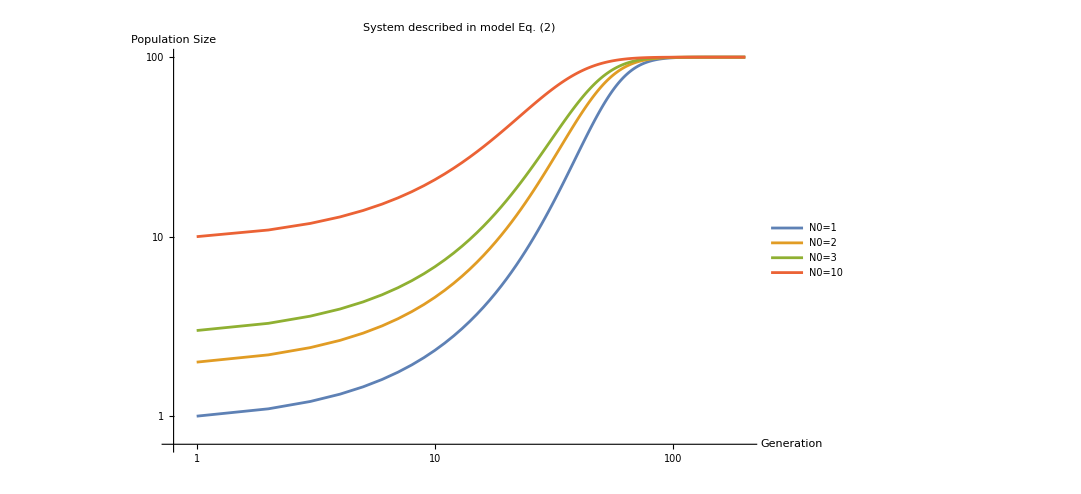

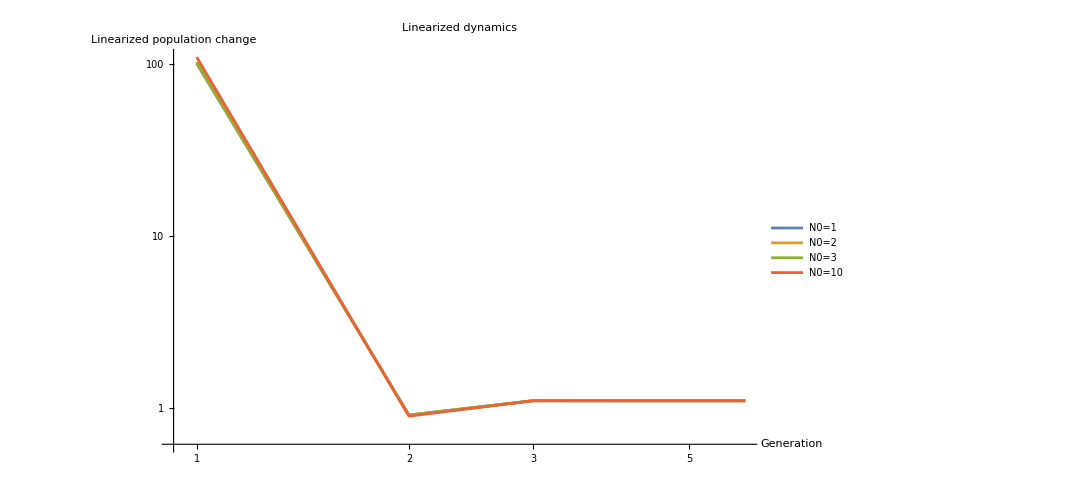

```mathematica
ClearAll["Global`*"];
K = 10^3;
r = 0.1;
b = 1;
N0values = {1,2,3,10};

evaluatedFP2 = K * r ^(1/b);
t0 = 0;
tMax = 200;

f2[n_] = n * (r+1) / (1 + (n/K)^b);
fLinear[n_] = -((-1-(n/K)^b+b (n/K)^b) (1+r))/((1+(n/K)^b)^2);

(* Iteravile evaluate the function f2 for tMax generations with the four different starting values of N0*)

resultsSystem = Table[
   NestList[f2, N0, tMax],
   {N0, N0values}
];

resultsLinearized  = Table[
   NestList[fLinear, evaluatedFP2+N0, tMax/40],
   {N0, N0values}
];


 ListLogLogPlot[resultsSystem, PlotRange -> All, 
 PlotLegends -> {"N0=1", "N0=2", "N0=3", "N0=10"},
 Joined -> True,
 PlotLabel->"System described in model Eq. (2)",
 AxesLabel -> {"Generation", "Population Size"},
 ImageSize -> {800, 600}]
 
  ListLogLogPlot[resultsLinearized, PlotRange -> All, 
 PlotLegends -> {"N0=1", "N0=2", "N0=3", "N0=10"},
 Joined -> True,
 PlotLabel->"Linearized dynamics",
  AxesLabel -> {"Generation", "Linearized population change"},
  ImageSize -> {800, 600}]
```

When checking the linearized dynamics (2nd plot), we see that after the 3rd generation we balance in at unity and therefore expect no more change in the population. On the other hand, in the 1st plot the exact population dynamics are shown. We can clearly see, that a steady state is approached after about 90 generations.
For the linearized dynamics it seems that all initial conditions approach the steady state equally fast. In the exact dynamics we clearly see, that this is not the case. =10 is certainly earlier approaching the steady population of  when for example compared with .

## e) Discuss how well the stability analysis approximates the exact dynamics. How does the initial condition influence the approximation?

As described in subtask d), the linearization seems to not give a clear representation of the dynamics. The difference of the tested initial condition seems to have no influence on how fast the steady state is approached. Where as in the exact dynamics there is a clear difference visible (especially well if looked at as a semilogY).

## f) Use linear stability analysis to approximate the dynamics in the vicinity of the stable steady state. Use initial population size N0 = N∗ +δN0, where N∗ is the value of the stable steady state and δN0 is an initial perturbation around N∗. Choose δN0 = −10, −3, −2, −1, 1, 2, 3 and 10. Proceed as follows. Starting from an initial perturbation δN0, approximate the dynamics until the system comes close to N∗ using the linear stability analysis around the stable steady state. Plot this approximation together with the exact dynamics, starting at N0. Perform the approximation for the different values of the initial perturbation δN0. How does the initial perturbation influence the approximation.

100.

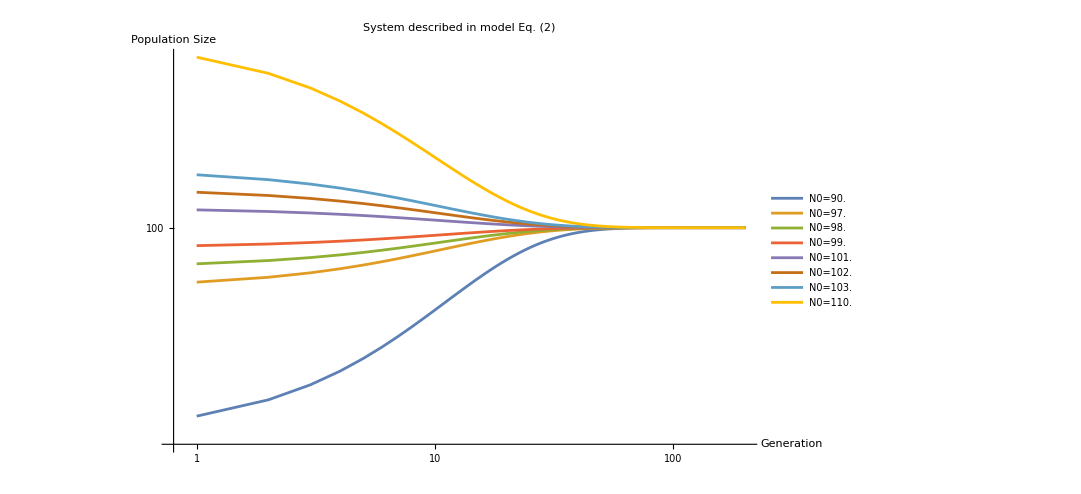

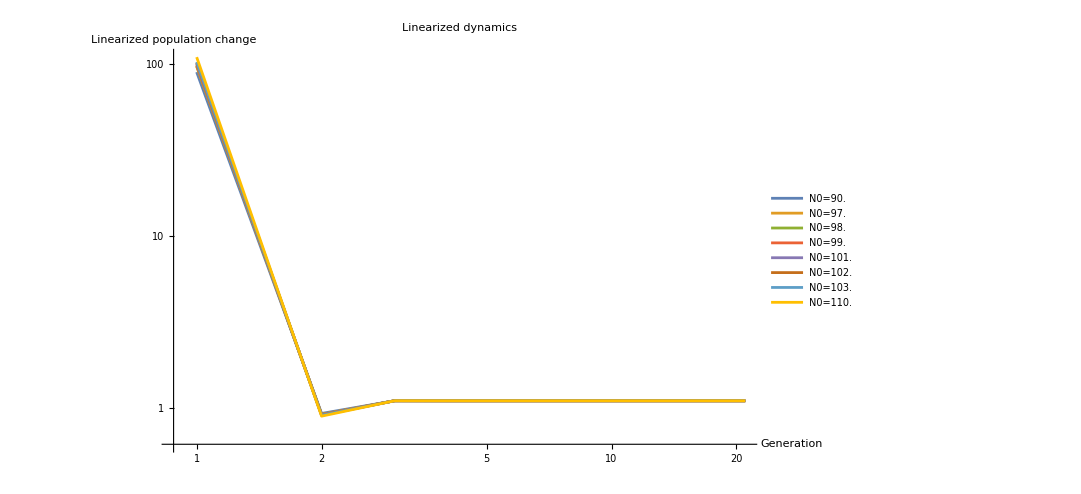

```mathematica
ClearAll["Global`*"];
K = 10^3;
r = 0.1;
b = 1;
DN0values = {-10,-3,-2,-1,1,2,3,10};
evaluatedFP2 = K * r ^(1/b)
N0Values = evaluatedFP2 + DN0values;


t0 = 0;
tMax = 200;

(* System from Eq 2*) 
f2[n_] = n * (r+1) / (1 + (n/K)^b);
(* Linearized system *) 
fLinear[n_] = -((-1-(n/K)^b+b (n/K)^b) (1+r))/((1+(n/K)^b)^2);

resultsSystem = Table[
   NestList[f2, N0, tMax],
   {N0, N0Values}
];

resultsLinearized  = Table[
   NestList[fLinear, N0 , tMax / 40],
   {N0, N0Values}
];

legendLabels = StringJoin["N0=", ToString[#]] & /@ N0Values;

 ListLogLogPlot[resultsSystem, PlotRange -> All, 
 PlotLegends -> legendLabels,
 Joined -> True,
 PlotLabel->"System described in model Eq. (2)",
 AxesLabel -> {"Generation", "Population Size"}, 
 ImageSize -> {800, 600}]
 
  ListLogLogPlot[resultsLinearized, PlotRange -> All, 
 PlotLegends -> legendLabels,
 Joined -> True,
 PlotLabel->"Linearized dynamics",
  AxesLabel -> {"Generation", "Linearized population change"},
  ImageSize -> {800, 600}]
```

A similar behaviour as in subtask d) is found. The linearized dynamics approach the value 1.1 very quickly, not depending from which initial condition the trajectory started. The exact solution approaches a steady state after about 90 generations, depending, here we do see a dependence on the intial condition. To be in steady state, would mean for the linearized dynamics to reach unity. As it doenst not reach it, it would suggest, that we dont reach a steady state.